```mathematica
f12={{0,1,0},{1,0,0},{0,0,0}};
f21={{0,-I,0},{I,0,0},{0,0,0}};
f13={{0,0,1},{0,0,0},{1,0,0}};
f31={{0,0,-I},{0,0,0},{I,0,0}};
u={{1,0,0},{0,-1,0},{0,0,-1}};
Id=IdentityMatrix[3];

Hint= KroneckerProduct[f12,f12,Id,Id,Id]+KroneckerProduct[f21,f21,Id,Id,Id]+KroneckerProduct[f13,f13,Id,Id,Id]+KroneckerProduct[f31,f31,Id,Id,Id]+KroneckerProduct[Id,f12,f12,Id,Id]+KroneckerProduct[Id,f21,f21,Id,Id]+KroneckerProduct[Id,f13,f13,Id,Id]+KroneckerProduct[Id,f31,f31,Id,Id]+KroneckerProduct[Id,Id,f12,f12,Id]+KroneckerProduct[Id,Id,f21,f21,Id]+KroneckerProduct[Id,Id,f13,f13,Id]+KroneckerProduct[Id,Id,f31,f31,Id]+KroneckerProduct[Id,Id,Id,f12,f12]+KroneckerProduct[Id,Id,Id,f21,f21]+KroneckerProduct[Id,Id,Id,f13,f13]+KroneckerProduct[Id,Id,Id,f31,f31];

Hid= KroneckerProduct[f12,f12,Id,Id,Id]+KroneckerProduct[f21,f21,Id,Id,Id]+KroneckerProduct[f13,f13,Id,Id,Id]+KroneckerProduct[f31,f31,Id,Id,Id]+√(3/2)(KroneckerProduct[Id,f12,f12,Id,Id]+KroneckerProduct[Id,f21,f21,Id,Id]+KroneckerProduct[Id,f13,f13,Id,Id]+KroneckerProduct[Id,f31,f31,Id,Id])+√(3/2)(KroneckerProduct[Id,Id,f12,f12,Id]+KroneckerProduct[Id,Id,f21,f21,Id]+KroneckerProduct[Id,Id,f13,f13,Id]+KroneckerProduct[Id,Id,f31,f31,Id])+KroneckerProduct[Id,Id,Id,f12,f12]+KroneckerProduct[Id,Id,Id,f21,f21]+KroneckerProduct[Id,Id,Id,f13,f13]+KroneckerProduct[Id,Id,Id,f31,f31];

g0=KroneckerProduct[Id,Id,Id,Id,Id];
g1=KroneckerProduct[u,Id,Id,Id,u];
```

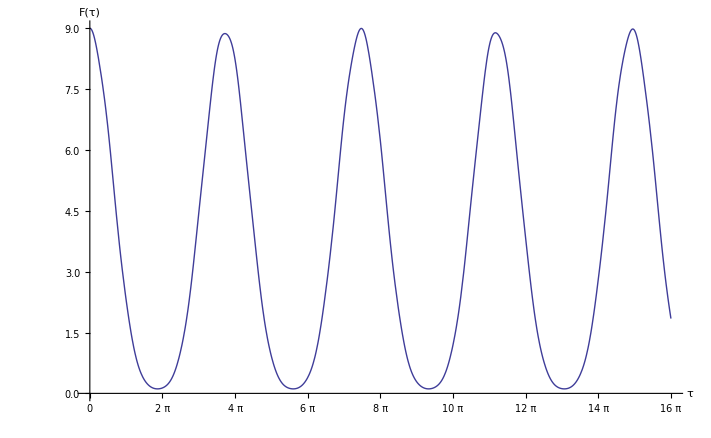

```mathematica
F[τ_]:=Abs[1/3^4 Tr[MatrixExp[I τ Hid].MatrixExp[-I τ Hint]]]^2
Plot[F[t],{t,0,16π},
AxesLabel->{"τ","F(τ)"},
Ticks->{Table[2π i,{i,0,8}],Automatic}]
```

```mathematica
Δt0=π/44;
N[Δt0]
Uid0=MatrixExp[I Δt0 Hid];
Uint0=N[MatrixExp[-I 11Δt0 Hint]];
G0[m_]:=Abs[1/3^4 Tr[MatrixPower[Uid0,m].MatrixPower[Uint0,m]]]^2
```

0.0713998

```mathematica
Uid1=MatrixExp[I 11 Δt0 Hid];
Uint1=N[MatrixExp[-I 10 Δt0 Hint].g1†.MatrixExp[-I Δt0 Hint].g1];
G1[m_]:=Abs[1/3^5 Tr[MatrixPower[Uid1,m].MatrixPower[Uint1,m]]]^2
```

$Aborted

```mathematica
FidelityPlot=
DiscretePlot[{G0[m],G1[m]},{m,0,10},
AxesLabel->{"(m π)/2","F(Δt,m)"},
Joined->True,
Filling->None,
PlotMarkers->{Automatic,Tiny},
PlotStyle->{Red,Darker@Green,Darker@Blue},
GridLines->Automatic]
```